```mathematica
Needs["DeepZot`CosmoTools`"]
```

```mathematica
createCosmology[Planck13]
```

```mathematica
SetDirectory["/Users/david/Cosmo/DESC/DarkEnergySchool/LargeScaleStructureStatistics/camb/"]
```

/Users/david/Cosmo/DESC/DarkEnergySchool/LargeScaleStructureStatistics/camb

```mathematica
exportToCamb["Planck13.camb",Planck13,redshifts->{0,1.2}]
```

Planck13.camb

```mathematica
Needs["DeepZot`PowerTools`"]
```

```mathematica
Pk=makePower[ReadList["Planck13_matterpower_1.dat",Number,RecordLists->True]];
```

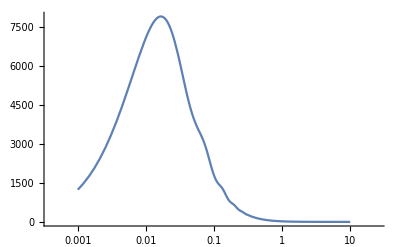

```mathematica
LogLinearPlot[Pk[k],{k,0.001,10}]
```